```mathematica
ClearAll["Global`*"]
```

Definition of objective functions

```mathematica
obj[{x_, y_}]:= 1/(a + Cos[b(x^2+y^2)]/(1+c(x^2 + y^2)));
obj2[{x_,y_}]:=20 Sin[π/2 (x-2 π)]+20 Sin[π/2 (y-2 π)]+(x-2 π)^2+(y-2 π)^2;
gpobj[{x_,y_}]:= (1+(x+y+1)^2*(19-14*x+3*x^2-14*y+6*x*y+3*y^2))*(30+(2*x-3*y)^2*(18-32*x+12*x^2+48*y-36*x*y+27*y^2));
michobj[{x_,y_}]:= Sin[x]*(Sin[x^2/Pi])^2+Sin[y]*(Sin[2*y^2/Pi])^2;
ackobj[{x_,y_}]:=-20*E^(-0.2*(1/2*(x^2+y^2))^(1/2))-E^(1/2*(Cos[2*Pi*x]+Cos[2*Pi*y]))+20+E
```

```mathematica
a = 1;
b = 5;
c = 10;


Plot3D[obj[{x,y}], {x, -Pi, Pi}, {y,-Pi, Pi},PlotRange->All]
Plot3D[obj2[{x,y}], {x, -Pi, Pi}, {y,-Pi, Pi},PlotRange->All]
Plot3D[michobj[{x,y}], {x, -Pi, Pi}, {y,-Pi, Pi},PlotRange->All]
Plot3D[ackobj[{x,y}], {x, -Pi, Pi}, {y,-Pi, Pi},PlotRange->All]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

Creation of individuals in the initial population, quantisation of {x,y}, and conversion from binary to decimal

```mathematica
createIndividual:= Table[RandomInteger[1],{i,1,2},{j,1,5}]
quant = 2*Pi/31;
binCoords[bin_List]:={FromDigits[bin[[1]],2]-31/2,FromDigits[bin[[2]],2]-31/2}*quant
```

```mathematica
testind=createIndividual
Head[testind]
FromDigits[testind[[1]],2]
Join[testind[[1]][[;;-3]],testind[[1]][[4;;]]]
```

{{1,1,0,0,0},{1,1,0,0,0}}

List

24

{1,1,0,0,0}

Creation of generation 0

```mathematica
popSize=3;
```

```mathematica
initPop[n_]:=Table[createIndividual,n]
testpop = initPop[popSize]
testpop2 = initPop[popSize]
```

{{{0,1,1,1,0},{1,0,0,1,1}},{{1,1,1,1,0},{0,0,0,1,1}},{{0,0,0,1,1},{0,1,0,1,1}}}

{{{0,1,0,0,1},{0,1,0,0,0}},{{0,1,0,1,1},{1,0,1,1,0}},{{1,0,0,0,0},{1,1,1,0,0}}}

Selection scheme: fitness proportionate selection

```mathematica
fitProp[pop_List, survivorNum_, cost_]:= Module[{sortPop, totObj,totFit, sortPopC, rand, selected},

sortPop=Sort[pop, cost[binCoords[#1]]<cost[binCoords[#2]]&];
sortPop =Table[{sortPop[[n]], N[cost[binCoords[sortPop[[n]]]]]},{n,1,Length[pop]}];
totObj = Sum[sortPop[[n, 2]], {n,popSize}];
sortPop = Table[{sortPop[[n,1]],E^(-0.5*sortPop[[n,2]]/totObj)}, {n,1,Length[pop]}];
totFit = Sum[sortPop[[n,2]],{n,popSize}];
sortPopC = Table[{sortPop[[n,1]], Sum[sortPop[[k,2]],{k,n}]},{n,1,Length[pop]}];


selected = {};

Do[
rand =  RandomReal[{0,totFit}];
selected = Append[selected, Select[sortPopC, #[[2]]>rand&,1]  [[1,1]] ];
,survivorNum];
Return [selected]
(*sortPop = accumulate obj and divide by totobj*)
]
```

```mathematica
obj[binCoords[testpop[[1]]]]
sortTest=fitProp[testpop,3, obj]

(*Table[{sortTest[[n]], N[obj[binCoords[sortTest[[n]]]]]},{n,1,popSize}][[1,2]]*)
```

1/(1+Cos[(290 π^2)/961]/(1+(580 π^2)/961))

sort

{{{1,1,1,1,0},{0,0,0,1,1}},{{0,0,0,1,1},{0,1,0,1,1}},{{0,1,1,1,0},{1,0,0,1,1}}}

popC

{{{{1,1,1,1,0},{0,0,0,1,1}},1.36983},{{{0,0,0,1,1},{0,1,0,1,1}},2.74175},{{{0,1,1,1,0},{1,0,0,1,1}},4.18819}}

Selected:

{{{0,0,0,1,1},{0,1,0,1,1}}}

Selected:

{{{0,0,0,1,1},{0,1,0,1,1}},{{0,0,0,1,1},{0,1,0,1,1}}}

Selected:

{{{0,0,0,1,1},{0,1,0,1,1}},{{0,0,0,1,1},{0,1,0,1,1}},{{1,1,1,1,0},{0,0,0,1,1}}}

{{{0,0,0,1,1},{0,1,0,1,1}},{{0,0,0,1,1},{0,1,0,1,1}},{{1,1,1,1,0},{0,0,0,1,1}}}

Crossover: single point (should inheritance completely from one parent be possible?)

```mathematica
singlePoint[{parentA_, parentB_}]:= Module[{pointX, pointY, child},
pointX = RandomInteger[{1,5}];
pointY = RandomInteger[{1,5}];

child = {Join[parentA[[1]][[;;pointX]],parentB[[1]][[pointX+1;;]]],Join[parentA[[2]][[;;pointY]],parentB[[2]][[pointY+1;;]]]};

Return[child]
]
```

```mathematica
singlePoint[{testpop[[1]],testpop[[2]]}]
```

{{0,1,1,1,0},{1,0,0,1,1}}

```mathematica
testind
{Join[testind[[1]][[;;-4]],testind[[1]][[4+1;;]]],Join[testind[[2]][[;;-5]],testind[[2]][[5+1;;]]]}
testind[[1]][[4;;]]
```

{{1,1,0,0,0},{1,1,0,0,0}}

{{1,1,0},{1}}

{0,0}

```mathematica
newPop[iter_, parents_]:=Module[{new},
new = {};
Do[
new = Append[new, Map[singlePoint,Partition[RandomSample[parents],2]]]; (*non-monogamous population*)
,iter];
Return[Flatten[new,1]]
]
```

Mutation: bit string (try using map???)

```mathematica
mutate[person_, rate_]:= Map[If[RandomReal[]*100<rate, 1-#,#]&,person,2]

(*For[i=1,i≤5,i++,If[RandomReal[]*100<rate, person[[*)
```

```mathematica
testind
mutate[testind,20]
```

{{1,1,0,0,0},{1,1,0,0,0}}

{{1,1,0,0,0},{0,0,1,0,1}}

Testing

```mathematica
averagefitness[pop_, cost_]:= Sum[cost[binCoords[pop[[n]]]],{n,1,Length[pop]}]/Length[pop];
fittestindividual[pop_, cost_]:=Sort[pop, cost[binCoords[#1]]>cost[binCoords[#2]]&][[1]];
dispgenes[pop_]:= ArrayPlot[Mean[pop], ImageSize->Tiny];
```

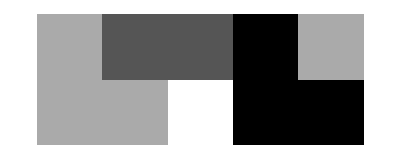

{{{0,2,1,1,1},{1,1,0,1,1}},{{1,2,1,2,1},{1,0,1,2,1}},{{1,0,0,1,1},{1,2,1,1,1}}}

```mathematica
dispgenes[testpop]
testpop+testpop2
```

Main body

```mathematica
population = initPop[10];
iters = 5;
mutationrate = 50;
fitlist = {};
Do[ (*training*)
breeders =fitProp[population,4,obj];

population = newPop[5,breeders];
population=Map[mutate[#,mutationrate]&, population, {1}];
(*need to cull? or adjust parameters for constant population?*)
mutationrate=mutationrate*0.95;
fitlist = Append[fitlist,averagefitness[population, obj]];
(*Print[N[averagefitness[population]]];
Print[N[fittestindividual[population]]];*)
,iters
]
(*Print[binCoords[fittestindividual[population]]]*)

Show[Plot3D[obj[{x,y}], {x, -Pi, Pi}, {y,-Pi, Pi},PlotRange->All, ColorFunction->"AvocadoColors"],
ListPointPlot3D[
{{binCoords[fittestindividual[population, obj]][[1]],binCoords[fittestindividual[population, obj]][[2]],N[obj[binCoords[fittestindividual[population, obj]]]]}}
,PlotRange->All]
	]

ListPlot[fitlist, Joined->True]
```

Nicely wrappered everything up

```mathematica
full[cost_,popsize_, initmutationrate_, iters_, scaling_:"None"]:=Module[{population,breeders,fitlist, mutationrate, fittest, pointz, scale},
population = initPop[popsize];
fitlist = {};
mutationrate = initmutationrate;
Do[ (*training*)
breeders =fitProp[population,Ceiling[0.4*popsize], cost];
population = newPop[Ceiling[0.5*popsize],breeders];
population=Map[mutate[#,mutationrate]&, population, {1}];
population = fitProp[population, popsize,cost];
(*need to cull? or adjust parameters for constant population?*)
mutationrate=mutationrate*0.95+10;
fitlist = Append[fitlist,averagefitness[population, cost]];
(*Print[N[averagefitness[population]]];
Print[N[fittestindividual[population]]];*)
,iters
];

fittest =binCoords[fittestindividual[population, cost]];
Print[fittest];
pointz = If[scaling == "Log10",Log10[N[cost[fittest]]],N[cost[fittest]]];
Show[Plot3D[cost[{x,y}], {x, -Pi, Pi}, {y,-Pi, Pi},PlotRange->All, ColorFunction->"AvocadoColors", ImageSize->Large, ScalingFunctions->If[scaling == "Log10","Log10",None]],
ListPointPlot3D[
{{fittest[[1]],fittest[[2]],pointz}}
,PlotRange->All]
	]
ListPlot[fitlist, Joined->True, PlotRange->All, ImageSize->Medium]
dispgenes[population]
]
```

{-π/31,π/31}

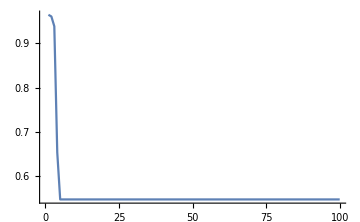
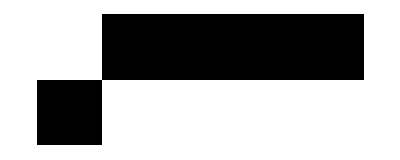
-Graphics- -Graphics- -Graphics3D-

```mathematica
full[obj,20, 50,100]
```

{(15 π)/31,(15 π)/31}

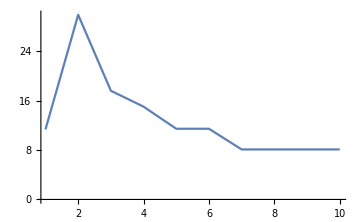
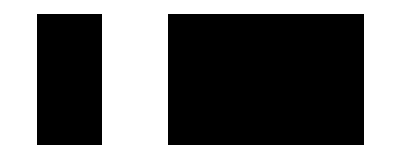
-Graphics- -Graphics- -Graphics3D-

```mathematica
full[obj2,20, 50,10]
```

{π/31,-(9 π)/31}

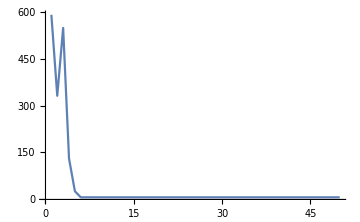
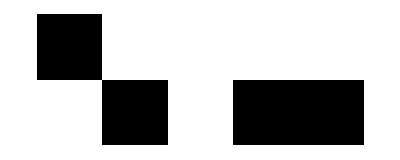
-Graphics- -Graphics- -Graphics3D-

```mathematica
full[gpobj,20, 50,50, "Log10"]
```

{π/31,π/31}

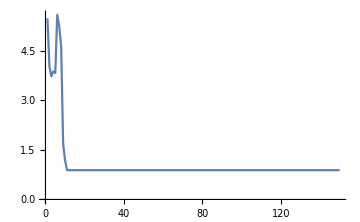
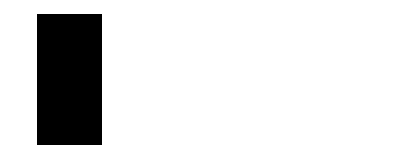
-Graphics- -Graphics- -Graphics3D-

```mathematica
full[ackobj,10, 20,150]
```

{-(19 π)/31,-(17 π)/31}

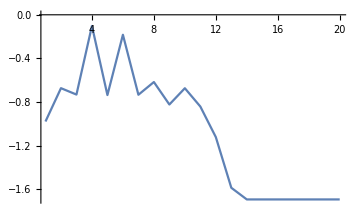
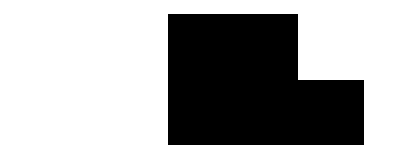
-Graphics- -Graphics- -Graphics3D-

```mathematica
full[michobj, 10, 20, 20]
```